```mathematica
ClearAll["Global`*"];
Remove["Global`*"];
```

```mathematica
results={};
sols={};
δvec=(Table[10^eδ,{eδ,-10,-2}]~Join~Table[δ,{δ,10^-1,9/10,1/10}]~Join~Table[δ,{δ,1,2,1/5}])//Reverse;
δvec={1/10}//Reverse;
δvec=(Table[10^eδ,{eδ,-3,-2}]~Join~Table[δ,{δ,10^-1,9/10,1/5}])//Reverse;
f0vec=Table[E^eδ,{eδ,-10,-10}]//Reverse;
f0vec={10^-15}//Reverse;
For[if0=1,if0≤Length[f0vec],if0+=1,
fixf0results={};
f0=f0vec[[if0]];
For[iδ=1,iδ≤Length[δvec],iδ+=1,
δ=δvec[[iδ]];
ϵ=10^-40;λ=Rationalize[638.5^2,0];k=Rationalize[1.2383 √λ,0];q=k(1-δ);
U[G_]:=G^2/12;a=1/(√6);
Ω[ϕ_,G_]:=k ((U[G]+1-a ϕ)-(1)E^(-a ϕ));
ς[ϕ_,G_]:=18((a Ω[ϕ,G]+D[Ω[ϕ,G], ϕ])^2+(D[Ω[ϕ,G], G])^2)-12 Ω[ϕ,G]^2-24k Ω[ϕ,G] (1)E^(-a ϕ);
dςdϕ[ϕ_,G_]:=12 a k^2 (2-(1)2 ⅇ^(-2 a ϕ)+(-2+3 a^2) (-U[G]+a ϕ));
dςdG[ϕ_,G_]:=-12 k^2 U'[G] (2+(-2+3 a^2) (-U[G]+a ϕ)-3 U''[G]);
eqn1=3(q z+1)(f'[z]β[z]+f[z](a ϕ'[z]β[z]+β'[z]))-12f[z] β[z]^2==ς[ϕ[z],G[z]]-(1)12 E^(-2a ϕ[z])k^2;
eqn2=6(a ϕ'[z]β[z]+β'[z])==(q z+1)((ϕ'[z])^2+(G'[z])^2);
eqn3=f[z](a(q z+1)(ϕ'[z])^2+(q-4β[z])ϕ'[z]+(q z+1)ϕ''[z])+(q z+1)f'[z]ϕ'[z]==1/(q z+1)(2a ς[ϕ[z],G[z]]+dςdϕ[ϕ[z],G[z]]);
eqn4=f[z](a(q z+1)ϕ'[z]G'[z]+(q-4β[z])G'[z]+(q z+1)G''[z])+(q z+1)f'[z]G'[z]==1/(q z+1)dςdG[ϕ[z],G[z]];
ic1=ϕ[ϵ]==D[√(8/3)λ(z+1/k)^2,{z,0}]/.z->ϵ;
ic2=ϕ'[ϵ]==D[√(8/3)λ(z+1/k)^2,{z,1}]/.z->ϵ;
ic3=G[ϵ]==D[√(24λ)(z+1/k),{z,0}]/.z->ϵ;
ic4=G'[ϵ]==D[√(24λ)(z+1/k),{z,1}]/.z->ϵ;
ic5=f[ϵ]==1;
ic6=β[ϵ]==Ω[ϕ[ϵ],G[ϵ]]+q E^(-a ϕ[ϵ]);
ϕExact[z_]:=√(8/3)λ(z+1/k)^2;
GExact[z_]:=√(24λ)(z+1/k);
fExact[z_]:=1;
βExact[z_]:=k ((U[GExact[z]]+1-a ϕExact[z])-E^(-a ϕExact[z]))+q E^(-a ϕExact[z]);
(*tmp=Reap[NDSolve[{eqn1,eqn2,eqn3,eqn4,ic1,ic2,ic3,ic4,ic5,ic6},{ϕ,G,f,β},{z,ϵ,100k},AccuracyGoal->∞,WorkingPrecision->50,MaxSteps->∞,Method->{"EventLocator", "Event"->f[z]-f0, "EventAction":>Sow[z]}]];
zHest=tmp[[2,1,1]];*)
factor=1-f0;
f0=E^-50;
tmp=Reap[NDSolve[{eqn1,eqn2,eqn3,eqn4,ic1,ic2,ic3,ic4,ic5,ic6},{ϕ,G,f,β},{z,ϵ,100k},AccuracyGoal->∞,WorkingPrecision->100,MaxSteps->∞,Method->{"EventLocator", "Event"->f[z]-f0, "EventAction":>Sow[z]}]];
sol=First[{ϕ,G,f,β}/.First[tmp]];
{zmin,zmax}=First[sol[[1]]["Domain"]];
zH=tmp[[2,1,1]];
zHest=factor zH;
A[z_]:=NIntegrate[(sol[[4]][zp])/(q zp+1),{zp,ϵ,z},MaxRecursion->1000000,Method->{"GlobalAdaptive",MaxErrorIncreases->10000},WorkingPrecision->50];
coeff=Exp[-3A[zH]];
coeffest=Exp[-3A[zHest]];
AppendTo[sols,sol];
Print[{1-δ,zH,k zH,-1/(4π)sol[[3]]'[zH],-1/(4π)sol[[3]]'[z]/.FindRoot[sol[[3]]''[z],{z,999/1000 zH},WorkingPrecision->30],zHest,-1/(4π)sol[[3]]'[zHest],coeff,coeffest}];
AppendTo[fixf0results,{1-δ,zH,k zH,-1/(4π)sol[[3]]'[zH],-1/(4π)sol[[3]]'[z]/.FindRoot[sol[[3]]''[z],{z,999/1000 zH},WorkingPrecision->30],zHest,-1/(4π)sol[[3]]'[zHest],coeff,coeffest}]];
AppendTo[results,fixf0results]]
```

NDSolve::ndsz: At z == 0.0001639744620302871398859261318243238406671148966483803844117458232055659933934511538032188856207903281, step size is effectively zero; singularity or stiff system suspected.

{1/10,0.0001639744620302871398858889587177320477597297682805230184864469527404004656504374304156263077042375239,0.1296471544880487649572645860049370092420476480614412009460433965178325969886370638484233312860554526,416.9053747047557702656605686141175750473519491046287543908670310028780190687,639.87041127245948761462508,0.0001639744620302869759114269284305921618707710505484752587566786722173819792034846900151606572668071083,483.72761600991592694144618860232684355030198269967233706301105386031181925292965946,0.08398716988336773214737918639948310523605498476912,0.1524919230432972669616914788329728514321442486401}

NDSolve::ndsz: At z == 0.0002008800936505836597942727394816208987616438941302898856877348622854853854214035602934997452305251431, step size is effectively zero; singularity or stiff system suspected.

{3/10,0.0002008800936505836597942345203884865986702639051600089636847044760762738850017668612029675373807789747,0.1588267600492600807719635873122246968526681063155295651780963594150720942228237268493447569324079789,404.83839832821427413030610337645862913427084993275462078628285801245532403888,576.360312434243730211528449,0.0002008800936505836597941957756434778445902826234912795228988147198299515610671001971998701345977304034,407.13527827284106904889049018316029893744213711273759597440671743908071330063,0.05231133686262860044580911802317795287512887761793,0.0539644048265465727001020656546156725148918563959}

NDSolve::ndsz: At z == 0.0002532165041578182452749988525441253206987078177343426636183494634015619643981690558298461565799760005, step size is effectively zero; singularity or stiff system suspected.

General::stop: Further output of NDSolve :: ndsz will be suppressed during this calculation.

{1/2,0.0002532165041578182452749592571349873632073007713835854367888483853884290659624575723855211205394721963,0.2002067811474729136996625377183977229123549481129416209108403651675149583554672087885666280756321466,390.2472667031581646839845055074753186084527173993978835398751381976118199105,522.65586265527809660414108,0.0002532165041578182452749104180055977285377268621763248417842182585505694892515940019688345843635940484,392.3681504563861749486033269925789314949278813189852565451845512317243029709,0.0295216788876151641193959975537176798464742505011,0.03073458394646025013500395832771494879689889694508}

{7/10,0.0003391069689101461196384534392554483330962693783331515495101641232564223879154213898146303524915364582,0.2681164679055155706569875667104688368524809720047776884597615352994511777271929370242611447655371372,363.5401389240205631855183180404661704752664142513231474523741976104759475502,475.4858611986485155174392,0.0003391069689101461196383880340039754381640015873521442134513061592472380195127683351549852604949359085,365.65957079406872758718209254658977652746005990849114991558962665289230329857,0.01365930654796162061744845154141052764044786933922,0.01439341843573127902095547022845040371382459752097}

{9/10,0.0005453009565735108481801119258655511772539705671787022747285106238061440974109132511439166810166979978,0.431144682434198761587964713694860726553708334505921616609446939435666148573581781672230428666750898,293.3716534996261922201703942361775620180345359207553563413551453252873448469,431.9528216872783535029802,0.0005453009565735108481800067509518426034557887865773820608186881809849839211007776328458241800500378849,296.2720865228771893869042205626576046973429808942068673353359858423121807531,0.003286793856449666269926746762743711516560877850408,0.003523072302235504104155243517901014253912685160109}

{99/100,0.001015397802053369057692866385217205674475231380383599506477660654026773965421184377366183579509064185,0.8028288922534955882940773100140364048096605532030736951743168694622446575818020943534900632741283637,176.9483368032988484121871568184631812176669004770857696578785101954858752767,421.2283342362293475343781,0.001015397802053369057692670540381572341289821818741496088599743493917226870448386200762485685151838878,181.1216525156492711556557059518656529090237440105108836737869341486076537975,0.0002520113053346126083201127046420583913677481906972,0.0002728649383814835773507195122353667348927222862787}

{999/1000,0.00146853648487236359212282913761838493353158459277865761899076440401180196273243827974403302514856996,1.161105053605340443366259016530552211348194926990342789347214284009969475533332758473792546683981265,119.71268916432642748391510033538098377874564544717280528727936086064545535796,440.564382464991275442057,0.001468536484872363592122545893666192229779023240037167826891741263177124334175418288004253698209355454,123.8961137333269032321117961132127043130807838648238620696565862168199267062,0.0000229590162693392953531973696387257810000524871608,0.0000248399151471165784742613045397343184622975789855}

{-0.999994089377426140002125444262855001512162015652900370381664766377853494944084119,-1.00000769243438354330136028231862895325162515118326769900706459556432630135216573,-1.0000058822267239954911186978549021578838191792016563231837882170462536378978945,-0.999986661706776111003457522217484391383953950647373287060880251408075975945491,-1.00000008701250241744651538757212951765949145701400319562979493063981552992316321,-0.99999205115417424242884329913449423076787081448093045556432514875548750576275894,-0.99998561521910669626153643182640123841832495482590337825146519291508779453018444}

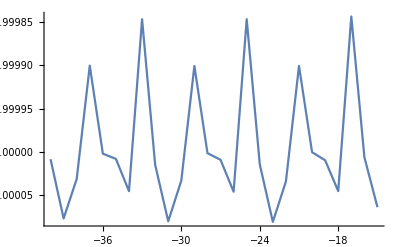

```mathematica
ϵpts=Table[E^lnϵ,{lnϵ,-40,-15}];
ϕpts=Table[sols[[i]][[1]][results[[;;,;;,2]][[1,i]]-#/q]&/@ϵpts,{i,Length[sols]}];
ϕppts=-q^-1 Table[sols[[i]][[1]]'[results[[;;,;;,2]][[1,i]]-#/q]&/@ϵpts,{i,Length[sols]}];
ϕpppts=q^-2 Table[sols[[i]][[1]]''[results[[;;,;;,2]][[1,i]]-#/q]&/@ϵpts,{i,Length[sols]}];
Table[Mean[(ϵpts*ϕpppts[[i]])/ϕppts[[i]]],{i,Length[sols]}]
ListLinePlot[{Log[ϵpts],(ϵpts*ϕpppts[[1]])/ϕppts[[1]]}//Transpose]
```

{-0.99395604643906566372661163116720849411482770674745159180617610844245743695641,-0.99381785455485532518549450830294447985376313205008078848053969750878781436221,-0.9936152894559246102624551326523550414671195047310937617252479788388837918281,-0.9931850198864278343333664872657292934357579399879446981659468573142072671823,-0.9917591564581469283413162542542675191073377322315455579037940492267919306618,-0.9872567403148367461928098071352867811832688474429000889590226952355846534141,-0.9825777998089626126846515693615852169628846440342486559941397592533900710179}

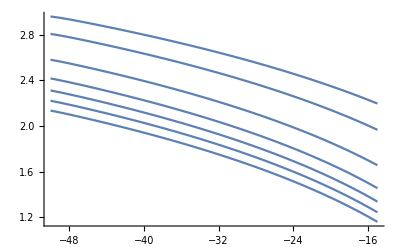

```mathematica
ϵpts=Table[E^lnϵ,{lnϵ,-50,-15}];
lnϕpts=Table[Log[sols[[i]][[1]][results[[;;,;;,2]][[1,i]]-#/q]]&/@ϵpts,{i,Length[sols]}];
ϕppts=-q^-1 Table[sols[[i]][[1]]'[results[[;;,;;,2]][[1,i]]-#/q]&/@ϵpts,{i,Length[sols]}];
ϕpppts=q^-2 Table[sols[[i]][[1]]''[results[[;;,;;,2]][[1,i]]-#/q]&/@ϵpts,{i,Length[sols]}];
Table[Mean[(ϵpts*ϕpppts[[i]])/ϕppts[[i]]],{i,Length[sols]}]
Show[Table[ListLinePlot[{Log[ϵpts],lnϕpts[[i]]}//Transpose],{i,Length[sols]}],PlotRange->All]
```

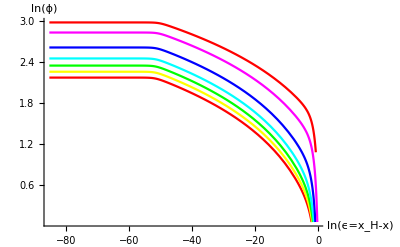

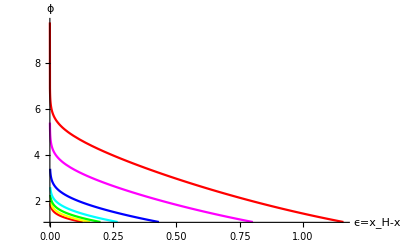

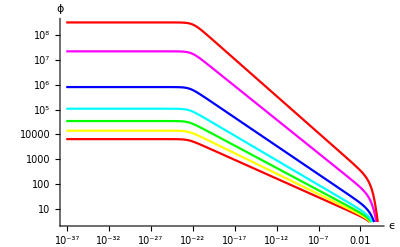

```mathematica
plotStyles=Table[Hue[Rescale[i,{1,Length[results[[1]]]}]],{i,Length[results[[1]]]}];
Show[Table[Plot[Log[(results[[;;,;;,2]][[1,i]]-E^lnx/q)(sols[[i]][[1]][results[[;;,;;,2]][[1,i]]-E^lnx/q])^-1 sols[[i]][[1]]'[results[[;;,;;,2]][[1,i]]-E^lnx/q]]//Evaluate,{lnx,Log[q ϵ],Log[q results[[;;,;;,2]][[1,i]]]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ϵ/ϕdϕ/dϵ",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All];
Show[Table[Plot[Log[sols[[i]][[1]][results[[;;,;;,2]][[1,i]]-E^lnx/q]]//Evaluate,{lnx,Log[q ϵ],Log[q results[[;;,;;,2]][[1,i]]]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(ϕ)",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
Show[Table[Plot[sols[[i]][[1]][results[[;;,;;,2]][[1,i]]-x/q]//Evaluate,{x,q ϵ,q results[[;;,;;,2]][[1,i]]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ϵ=x_H-x",16],Style["ϕ",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
Show[Table[LogLogPlot[sols[[i]][[1]][results[[;;,;;,2]][[1,i]]-x/q]//Evaluate,{x,q ϵ,q results[[;;,;;,2]][[1,i]]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ϵ",16],Style["ϕ",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
```

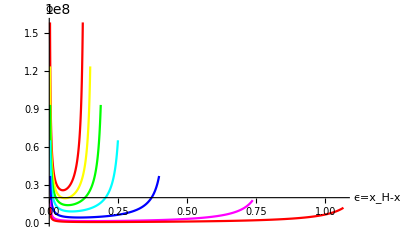

```mathematica
Show[Table[Plot[(results[[;;,;;,2]][[1,i]]-x/q)^-1(sols[[i]][[1]]'[results[[;;,;;,2]][[1,i]]-x/q])/(sols[[i]][[1]][results[[;;,;;,2]][[1,i]]-x/q])//Evaluate,{x,q ϵ,q results[[;;,;;,2]][[1,i]]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ϵ=x_H-x",16],Style["ϕ",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
```

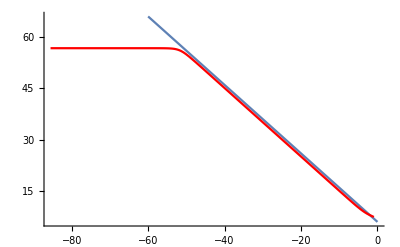

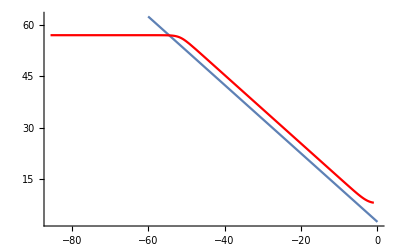

```mathematica
plotStyles=Table[Hue[Rescale[i,{1,Length[results]}]],{i,Length[results]}];
Show[Table[Plot[Log[sols[[i]][[3]][results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(f)",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All];
Show[Plot[8.725+0.02x,{x,-60,0}],Table[Plot[Log[sols[[i]][[3]]'[results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]//Abs]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(|f'|)",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All];
Show[Plot[11.4-0.98x,{x,-60,0}],Table[Plot[Log[sols[[i]][[3]]''[results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]//Abs]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(|f'|)",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All];
Show[Plot[6-x,{x,-60,0}],Table[Plot[Log[sols[[i]][[1]]'[results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]//Abs]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ϕ",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
Show[Plot[√6-x,{x,-60,0}],Table[Plot[Log[sols[[i]][[2]]'[results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]//Abs]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ϕ",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
```

```mathematica
k//N
q//N
```

790.655

79.0655

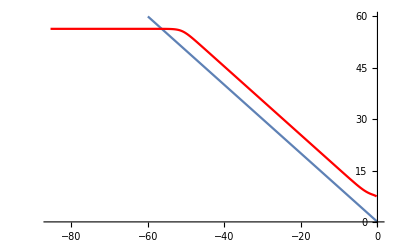

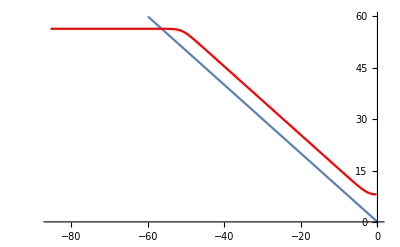

```mathematica
Show[Plot[-1x,{x,-60,0}],Table[Plot[Log[sols[[i]][[1]]'[results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]//Abs]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(|ϕ'|)",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
Show[Plot[-1x,{x,-60,0}],Table[Plot[Log[sols[[i]][[2]]'[results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]//Abs]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(|G'|)",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
```

```mathematica
Plot[1/2-6.5^-1 x,{x,-60,0}]
Plot[3-4^-1 x,{x,-60,0}]
```

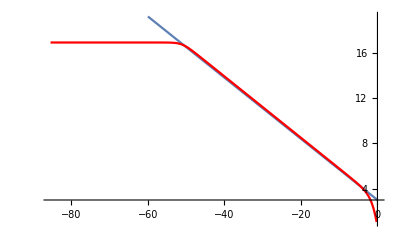

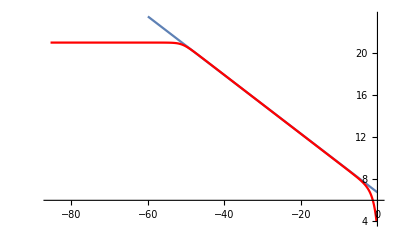

```mathematica
Show[Plot[3-3.7^-1 x,{x,-60,0}],Table[Plot[sols[[i]][[1]][results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ϕ",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
Show[Plot[6.75-3.6^-1 x,{x,-60,0}],Table[Plot[sols[[i]][[2]][results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["G",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
```

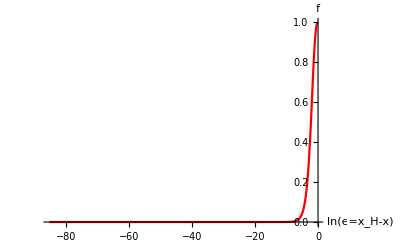

```mathematica
Show[Table[Plot[sols[[i]][[3]][results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],PlotRange->All,AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["f",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
```

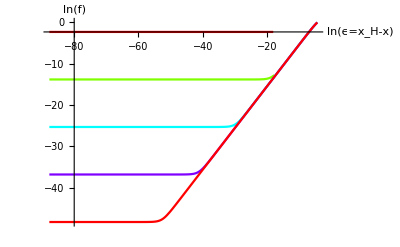

```mathematica
plotStyles=Table[Hue[Rescale[i,{1,Length[results]}]],{i,Length[results]}];
Show[Table[Plot[Log[sols[[i]][[3]][results[[;;,;;,2]][[i,1]]-(E^lnx-1+1)/q]]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[i,1]]-1]},PlotStyle->plotStyles[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(f)",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
```

```mathematica
E^-18.
```

1.523×10^-8

```mathematica
q zH+1
```

1.01296471544880487649558269576245106010638880167059

```mathematica
ListLinePlot[Table[results[[i,;;,{1,3}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["z_H",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
ListLinePlot[Table[results[[i,;;,{1,4}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["T (MeV)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
ListLinePlot[Table[results[[i,;;,{1,6}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["s/(8πM^3)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
ListLinePlot[Table[results[[i,;;,{4,6}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["T (MeV)",16],Style["s/(8πM^3)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
ListLinePlot[Table[results[[i,;;,{1,5}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["q/k",16],Style["T (MeV)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
ListLinePlot[Table[results[[i,;;,{5,6}]],{i,Length[results]}],PlotRange->All,AxesLabel->{Style["T (MeV)",16],Style["s/(8πM^3)",16]},PlotStyle->plotStyles,PlotLegends->plotLegends]
```

```mathematica
Export["stable_zH_vs_qByk.pdf",%]
Export["unstable_T_vs_qByk.pdf",%]
Export["stable_s_vs_qByk.pdf",%]
Export["unstable_s_vs_T.pdf",%]
Export["stable_T_vs_qByk.pdf",%]
Export["stable_s_vs_T.pdf",%]
```

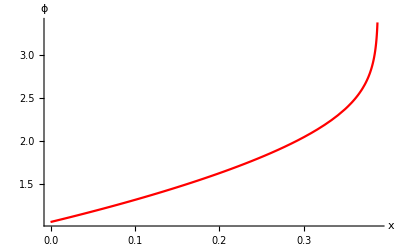

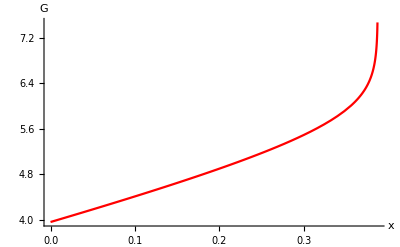

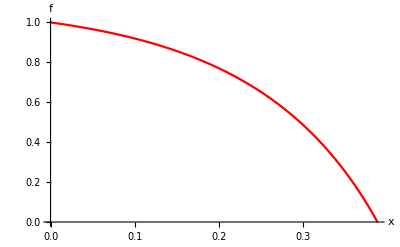

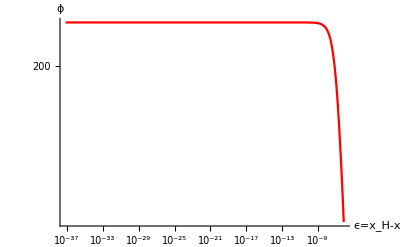

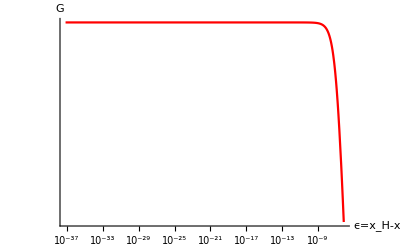

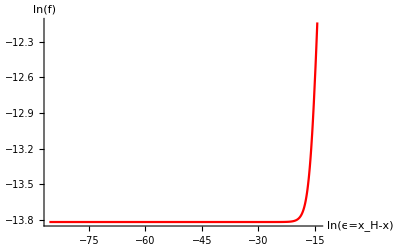

```mathematica
plotStyles=Table[Hue[Rescale[i,{1,Length[sols]}]],{i,Length[sols]}];
plotLegends=Table[StringForm["q/k=``",results[[;;,;;,1]][[1,i]]],{i,Length[sols]}];
Show[Table[Plot[sols[[i]][[1]][(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["x",16],Style["ϕ",16]}],{i,Length[sols]}],PlotRange->All]
Show[Table[Plot[sols[[i]][[2]][(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["x",16],Style["G",16]}],{i,Length[sols]}],PlotRange->All]
Show[Table[Plot[sols[[i]][[3]][(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["x",16],Style["f",16]}],{i,Length[sols]}],PlotRange->All]
Show[Table[LogLogPlot[sols[[i]][[1]][results[[;;,;;,2]][[1,i]]-(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["ϵ=x_H-x",16],Style["ϕ",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
Show[Table[LogLogPlot[sols[[i]][[2]][results[[;;,;;,2]][[1,i]]-(x-1+1)/q]//Evaluate,{x,1+q ϵ-1,1+q results[[;;,;;,2]][[1,i]]-1},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["ϵ=x_H-x",16],Style["G",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
Show[Table[Plot[Log[sols[[i]][[3]][results[[;;,;;,2]][[1,i]]-(E^lnx-1+1)/q]]//Evaluate,{lnx,Log[1+q ϵ-1],Log[1+q results[[;;,;;,2]][[1,i]]-1]},PlotStyle->plotStyles[[i]],PlotLegends->plotLegends[[i]],AxesLabel->{Style["ln(ϵ=x_H-x)",16],Style["ln(f)",16]},WorkingPrecision->100],{i,Length[sols]}],PlotRange->All]
```